```mathematica
(*Import packages*)
(*<< PVReduce`*)
(*Remove[PVReduce`Dot];*)
$LoadFeynArts = True;
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<<TreeLevel`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
(*Why is this?*)
$KeepLogDivergentScalelessIntegrals=True;
```

## Get Feynman diagrams

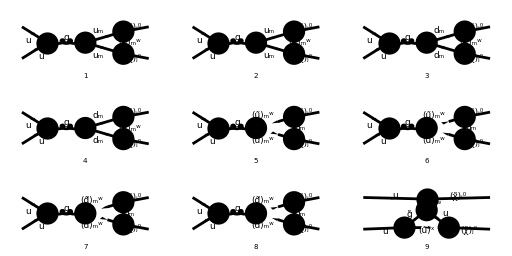

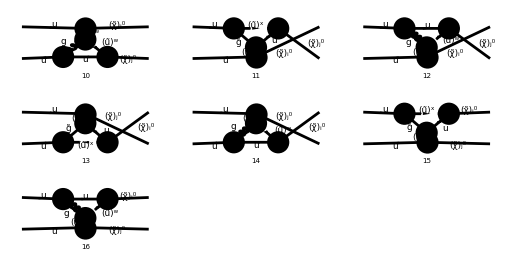

```mathematica
triDiagrams = InsertFields[CreateTopologies[1, 2->2,ExcludeTopologies->{Boxes,SelfEnergies,Tadpoles}], {F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD,Restrictions->{NoLightFHCoupling,NoElectronHCoupling},ExcludeParticles->{V[1],V[2],V[3],F[11],F[12],S[1],S[2],S[3],S[4]}];
Paint[triDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

## Convert diagrams to amplitudes

```mathematica
(*Box-loop diagrams*)
Subscript[M, tri][0]=FCFAConvert[CreateFeynAmp[triDiagrams], IncomingMomenta->{p1,p2}, OutgoingMomenta->{pi,pj},LoopMomenta->{qloop},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν}]//.AmpSimplifyRules;
```

FCFAConvert::sumOverWarn: You are omitting SumOver objects that may represent a nontrivial summation. This may lead to a loss of overall factors multiplying some of your diagrams. Please make sure that this is really what you want.

```mathematica
(*Replacing couplings*)
Subscript[M, tri][1]=Subscript[M, tri][0]//.QSimplifyRules//Simplify;
```

```mathematica
Subscript[M, tri][2]=TraceLoopAmp/@Subscript[M, tri][1];
```

```mathematica
Subscript[M, tri][3]=EvalPVLoopAmp/@SparseArray[Subscript[M, tri][2]]["NonzeroValues"];
CheckPVRemainder/@Subscript[M, tri][3]
```

{True,True,True,True,True,True,True,True}

```mathematica
(*CheckPVRemainder/@Subscript[M, tri][2]
Part[Subscript[M, tri][3],1]
(Collect2[#1,B0,C0,D0]&)/@(TrickMandelstam[#1,MandelstamParameters]&)/@(TID[#1,qloop,ToPaVe->True]&)/@(SelectFree2[#1,{A0,B0,C0,D0}]&)/@Subscript[M, tri][2]*)
```

```mathematica
PossibleZeroQ[SelectNotFree2[Part[Subscript[M, tri][3],1],C0]]
```

False

```mathematica
Subscript[M, tri][4]=Select[(SelectNotFree2[#1,{A0,B0,C0,D0}]&)/@Select[Subscript[M, tri][3],CheckPVRemainder],(!PossibleZeroQ[#1-1]&)]
```

## Compute interference with tree-level amplitudes

```mathematica
(Prefactor FullSimplify[SelectFree2[#1,DiracTrace]/Prefactor]&)/@Subscript[I, ttri][0]
```

{1/(2 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_i^2) (B_0(m_j^2,0,m_((q̃)_C)^2) m_j (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))-m_j (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))+C_0(0,t,m_j^2,m_((q̃)_C)^2,m_(g̃)^2,0) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))-(m_(g̃)^2 m_j^2-t m_((q̃)_C)^2) (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))+B_0(t,0,m_(g̃)^2) (Conjugate[((Q̃)_(A,1))] C_jC^L (-m_(g̃) Conjugate[((Q̃)_(C,1))] m_j (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2+t Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(C,2))] C_iA^L+t Conjugate[(C_iA^R)] Conjugate[((Q̃)_(C,2))] Q_B^(R R̄))+Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] (-m_(g̃) Conjugate[((Q̃)_(C,2))] m_j (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄)) (Conjugate[SqrtEGl])^2+t Conjugate[(Q_B^(L L̄))] Conjugate[((Q̃)_(C,1))] C_iA^L+t Conjugate[(C_iA^R)] Conjugate[((Q̃)_(C,1))] Q_B^RL))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (t-m_i^2) (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (t-m_j^2)-B_0(t,0,m_((q̃)_A)^2) (m_j^2+t)-2 C_0(0,t,m_j^2,0,0,m_((q̃)_A)^2) (t-m_j^2) (m_j^2-m_((q̃)_A)^2)) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))) g_s^2 g_W^4 δ_ab)/(4 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2)),1/(4 π^2 (u-m_j^2)^2 (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(0,m_(g̃)^2,m_((q̃)_C)^2) (m_j^2-u) (Conjugate[SqrtEGl] (Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) m_i-Conjugate[(Q_B^LR)] C_iA^R tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) m_j) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,1)+SqrtEGl (Conjugate[(C_iA^L)] tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) m_j Q_B^RL-C_iA^R tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) m_i Q_B^(R R̄)) (m_(g̃) SqrtEGl C_jC^R (Q̃)_(A,2)-Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)) (Q̃)_(C,2))+C_0(u,m_j^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (m_(g̃) C_jC^R (Conjugate[(C_iA^L)] m_j (2 (u-m_j^2) (t u-m_i^2 m_j^2) (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u)-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u))) Q_B^RL-C_iA^R m_i ((tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2-m_j^2+u)+2 s (u-m_j^2) (m_(g̃)^2+m_j^2-u)) m_j^2+(2 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) m_((q̃)_C)^2) Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^L)] (Conjugate[(Q_B^LR)] C_iA^R m_j (2 (u-m_j^2) (t u-m_i^2 m_j^2) (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u)+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u)))+Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i (2 s m_j^6-(tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)+2 s (-m_(g̃)^2+m_((q̃)_C)^2+2 u)) m_j^4+(tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+u)+2 s u (-m_(g̃)^2+m_((q̃)_C)^2+u)) m_j^2+u tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) m_((q̃)_C)^2)) (Q̃)_(A,1) (Q̃)_(C,1)+Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jC^R m_i m_j (2 s (u-m_j^2) (m_(g̃)^2 m_j^2-u m_((q̃)_C)^2)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u))) (Q̃)_(A,2) (Q̃)_(C,1)-Conjugate[(C_jC^L)] (2 m_(g̃)^2 m_i^2 m_j^6-u (2 t m_(g̃)^2+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 m_i^2 (m_(g̃)^2+m_((q̃)_C)^2)) m_j^4+u (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+u)+2 u (t m_(g̃)^2+(m_i^2+t) m_((q̃)_C)^2)) m_j^2+u^2 (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)-2 t u) m_((q̃)_C)^2) Q_B^RL (Q̃)_(A,1) (Q̃)_(C,2))+C_iA^R (Conjugate[(Q_B^LR)] C_jC^R (-2 m_(g̃)^2 m_i^2 m_j^6+u (2 t m_(g̃)^2-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 m_i^2 (m_(g̃)^2+m_((q̃)_C)^2)) m_j^4+u (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+u)-2 u (t m_(g̃)^2+(m_i^2+t) m_((q̃)_C)^2)) m_j^2+u^2 (2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) (Q̃)_(A,2) (Q̃)_(C,1)-Conjugate[(C_jC^L)] m_i m_j (2 s (u-m_j^2) (u m_((q̃)_C)^2-m_(g̃)^2 m_j^2)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u))) Q_B^(R R̄) (Q̃)_(A,1) (Q̃)_(C,2)))+B_0(m_j^2,0,m_((q̃)_C)^2) m_j (m_(g̃) Conjugate[(C_jC^L)] (2 Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i m_j (s m_j^2-s u-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(Q_B^LR)] C_iA^R (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)+2 (u-m_j^2) (t u-m_i^2 m_j^2))) (Q̃)_(A,1) (Q̃)_(C,1) (Conjugate[SqrtEGl])^2-C_iA^R (2 Conjugate[(Q_B^LR)] C_jC^R m_j (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+(u-m_j^2) (t u-m_i^2 m_j^2)) (Q̃)_(A,2) (Q̃)_(C,1)+m_i Q_B^(R R̄) (Conjugate[(C_jC^L)] (2 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) (Q̃)_(A,1)-2 m_(g̃) SqrtEGl^2 C_jC^R m_j (s m_j^2-s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,2)) (Q̃)_(C,2))+Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jC^R m_i (2 s (u-m_j^2) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) (Q̃)_(A,2) (Q̃)_(C,1)-Q_B^RL (m_(g̃) C_jC^R (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)-2 (u-m_j^2) (t u-m_i^2 m_j^2)) (Q̃)_(A,2) SqrtEGl^2+2 Conjugate[(C_jC^L)] m_j ((u-m_j^2) (t u-m_i^2 m_j^2)-u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,1)) (Q̃)_(C,2)))+B_0(u,0,m_(g̃)^2) (m_(g̃) Conjugate[(C_jC^L)] (Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i (2 s (u-m_j^2) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u))-2 Conjugate[(Q_B^LR)] C_iA^R m_j (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+(u-m_j^2) (t u-m_i^2 m_j^2))) (Q̃)_(A,1) (Q̃)_(C,1) (Conjugate[SqrtEGl])^2+u Conjugate[(Q_B^LR)] C_iA^R C_jC^R (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)+2 (u-m_j^2) (t u-m_i^2 m_j^2)) (Q̃)_(A,2) (Q̃)_(C,1)-C_iA^R m_i Q_B^(R R̄) (m_(g̃) C_jC^R (2 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) (Q̃)_(A,2) SqrtEGl^2+2 u Conjugate[(C_jC^L)] m_j (-s m_j^2+s u-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,1)) (Q̃)_(C,2)-Conjugate[(C_iA^L)] (2 u Conjugate[(Q_B^(L L̄))] C_jC^R m_i m_j (-s m_j^2+s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,2) (Q̃)_(C,1)+Q_B^RL (2 m_(g̃) C_jC^R m_j ((u-m_j^2) (t u-m_i^2 m_j^2)-u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,2) SqrtEGl^2+u Conjugate[(C_jC^L)] (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)-2 (u-m_j^2) (t u-m_i^2 m_j^2)) (Q̃)_(A,1)) (Q̃)_(C,2)))),1/(8 π^2 (u-m_j^2)^2 (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (2 B_0(0,0,0) (u-m_j^2) (Conjugate[(Q_B^LR)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_A^RL-Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j (-2 s m_j^2+2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_jA^R)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)-2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_B^RL)+m_i m_j (2 s m_j^2-2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_A^(R R̄) Q_B^(R R̄))-2 C_0(u,m_j^2,0,0,m_((q̃)_A)^2,0) (u-m_j^2) (m_j^2-m_((q̃)_A)^2) (Conjugate[(Q_B^LR)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_A^RL-Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j (-2 s m_j^2+2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_jA^R)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)-2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_B^RL)+m_i m_j (2 s m_j^2-2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_A^(R R̄) Q_B^(R R̄))+B_0(u,0,m_((q̃)_A)^2) (-Conjugate[(Q_B^LR)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)+2 (t u-m_i^2 m_j^2) (u^2-m_j^4)) Q_A^RL+Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)+2 s (u^2-m_j^4))+Conjugate[(C_jA^R)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)-2 (t u-m_i^2 m_j^2) (u^2-m_j^4)) Q_B^RL)-m_i m_j (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)+2 s (m_j^4-u^2)) Q_A^(R R̄) Q_B^(R R̄))+B_0(m_j^2,0,m_((q̃)_A)^2) m_j (Conjugate[(C_iA^L)] (Conjugate[(C_jA^R)] m_j (4 (u-m_j^2) (t u-m_i^2 m_j^2)-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)) Q_B^RL-Conjugate[(Q_B^(L L̄))] C_jA^L m_i (4 s (u-m_j^2) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)))+C_iA^R (Conjugate[(Q_B^LR)] C_jA^L m_j (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)+4 (u-m_j^2) (t u-m_i^2 m_j^2))+Conjugate[(C_jA^R)] m_i (4 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)) Q_B^(R R̄)))) g_s^2 g_W^4 δ_ab,1/(4 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (B_0(u,0,m_(g̃)^2) (Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(C,2))] C_jA^L (u Conjugate[((Q̃)_(A,1))] C_iC^L-m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] m_i) (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))-Conjugate[((Q̃)_(C,1))] (u Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))]-m_(g̃) SqrtEGl^2 Conjugate[((Q̃)_(A,1))] C_iC^L m_i) (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+2 s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(C,2))] m_i (m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] m_i-u Conjugate[((Q̃)_(A,1))] C_iC^L) m_j Q_B^(R R̄))+B_0(m_i^2,0,m_((q̃)_C)^2) m_i (m_(g̃) Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Q_B^LR)] C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))-2 s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄)) (Conjugate[SqrtEGl])^2+Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L m_i (2 m_i^2 m_j^2-2 t u-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))-Conjugate[((Q̃)_(C,1))] (m_(g̃) SqrtEGl^2 Conjugate[((Q̃)_(A,1))] C_iC^L-Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] m_i) (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+2 s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i^2 m_j Q_B^(R R̄))+C_0(0,u,m_i^2,m_((q̃)_C)^2,m_(g̃)^2,0) (m_(g̃) Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) (Conjugate[(Q_B^LR)] C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))-2 s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄)) (Conjugate[SqrtEGl])^2+Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) (u m_((q̃)_C)^2-m_(g̃)^2 m_i^2)-Conjugate[((Q̃)_(C,1))] (m_(g̃) Conjugate[((Q̃)_(A,1))] C_iC^L m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) SqrtEGl^2+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] (u m_((q̃)_C)^2-m_(g̃)^2 m_i^2)) (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+2 s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i m_j (m_(g̃)^2 m_i^2-u m_((q̃)_C)^2) Q_B^(R R̄))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (u-m_i^2)-B_0(u,0,m_((q̃)_A)^2) (m_i^2+u)-2 C_0(0,u,m_i^2,0,0,m_((q̃)_A)^2) (u-m_i^2) (m_i^2-m_((q̃)_A)^2)) (Conjugate[(Q_B^LR)] (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_A^RL-Conjugate[(C_iA^L)] (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)-2 s m_i m_j Q_A^(R R̄) Q_B^(R R̄)) g_s^2 g_W^4 δ_ab)/(8 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2)),1/(4 π^2 (t-m_i^2)^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_j^2) g_s^2 g_W^4 δ_ab (B_0(0,m_(g̃)^2,m_((q̃)_C)^2) (tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (t-m_i^2) (C_iC^R (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (Q̃)_(A,2) (Q̃)_(C,1)-Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,1) (Q̃)_(C,2))+B_0(t,0,m_(g̃)^2) (-2 m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) m_i (Q̃)_(A,1) (Q̃)_(C,1) (t-m_i^2)^2-2 m_(g̃) SqrtEGl^2 C_iC^R m_i (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) (t-m_i^2)^2+C_iC^R (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (2 t (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (m_i^2+t)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_i^2+t)) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_iC^L)] (2 t (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (m_i^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_i^2+t)) (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,1) (Q̃)_(C,2))+2 B_0(m_i^2,0,m_((q̃)_C)^2) m_i (Conjugate[SqrtEGl] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1) (t-m_i^2)^2+SqrtEGl C_iC^R m_i (-(t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,2)) (Q̃)_(C,1)-SqrtEGl (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i ((t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,1)-m_(g̃) SqrtEGl C_iC^R (t-m_i^2)^2 (Q̃)_(A,2)) (Q̃)_(C,2))+C_0(t,m_i^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (2 m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Q̃)_(A,1) (Q̃)_(C,1) (t-m_i^2)^2+2 m_(g̃) SqrtEGl^2 C_iC^R m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) (t-m_i^2)^2+Conjugate[(C_jA^L)] (Conjugate[(C_iC^L)] (-2 m_(g̃)^2 m_i^6-(tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)-2 t (2 m_(g̃)^2+m_((q̃)_C)^2)) m_i^4+(-2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) Q_B^RL (Q̃)_(A,1) (Q̃)_(C,2)-Conjugate[(Q_B^(L L̄))] C_iC^R (2 m_(g̃)^2 m_i^6-(4 t m_(g̃)^2+2 t m_((q̃)_C)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_i^4+(2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (-2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) (Q̃)_(A,2) (Q̃)_(C,1))+C_jA^R (Conjugate[(C_iC^L)] (-2 m_(g̃)^2 m_i^6-(tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)-2 t (2 m_(g̃)^2+m_((q̃)_C)^2)) m_i^4+(-2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) Q_B^(R R̄) (Q̃)_(A,1) (Q̃)_(C,2)-Conjugate[(Q_B^LR)] C_iC^R (2 m_(g̃)^2 m_i^6-(4 t m_(g̃)^2+2 t m_((q̃)_C)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_i^4+(2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (-2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) (Q̃)_(A,2) (Q̃)_(C,1)))),1/(8 π^2 (t-m_i^2)^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_j^2) (2 B_0(m_i^2,0,m_((q̃)_A)^2) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄))) m_i^2-B_0(t,0,m_((q̃)_A)^2) (m_i^2+t) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄)))+B_0(0,0,0) (t-m_i^2) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄)))-C_0(t,m_i^2,0,0,m_((q̃)_A)^2,0) (t-m_i^2) (m_i^2-m_((q̃)_A)^2) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄)))) g_s^2 g_W^4 δ_ab}

```mathematica
(*Subscript[I, stri][0]=SquareAmplitudes[ReplaceAll[Subscript[M, tri][4],{Index[Sfermion,5]->A,Index[Sfermion,6]->C}],Subscript[M̄, s][0]]//.SuperChargeRules*)
Subscript[I, ttri][0]=FullSimplify/@SquareAmplitudes[ReplaceAll[Subscript[M, tri][4],{Index[Sfermion,5]->A,Index[Sfermion,6]->C}],ReplaceAll[Subscript[M̄, t][0],A->B]]//.{SqrtEGl Conjugate[SqrtEGl]->1}//.SuperChargeRules
(*Subscript[I, utri][0]=SquareAmplitudes[ReplaceAll[Subscript[M, tri][4],{Index[Sfermion,5]->A,Index[Sfermion,6]->C}],ReplaceAll[Subscript[M̄, u][0],A->B]]//.SuperChargeRules*)
```

{1/(2 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_i^2) (B_0(t,0,m_(g̃)^2) (-m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L m_j (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2-m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))+t (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))+B_0(m_j^2,0,m_((q̃)_C)^2) m_j (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))-m_j (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))+C_0(0,t,m_j^2,m_((q̃)_C)^2,m_(g̃)^2,0) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))-(m_(g̃)^2 m_j^2-t m_((q̃)_C)^2) (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (t-m_i^2) (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (t-m_j^2)-B_0(t,0,m_((q̃)_A)^2) (m_j^2+t)-2 C_0(0,t,m_j^2,0,0,m_((q̃)_A)^2) (t-m_j^2) (m_j^2-m_((q̃)_A)^2)) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))) g_s^2 g_W^4 δ_ab)/(4 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2)),1/(4 π^2 (u-m_j^2)^2 (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(0,m_(g̃)^2,m_((q̃)_C)^2) (m_j^2-u) (Conjugate[SqrtEGl] (Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) m_i-Conjugate[(Q_B^LR)] C_iA^R tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) m_j) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,1)+SqrtEGl (Conjugate[(C_iA^L)] tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) m_j Q_B^RL-C_iA^R tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) m_i Q_B^(R R̄)) (m_(g̃) SqrtEGl C_jC^R (Q̃)_(A,2)-Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)) (Q̃)_(C,2))+B_0(m_j^2,0,m_((q̃)_C)^2) m_j (m_(g̃) C_jC^R (Conjugate[(C_iA^L)] (2 (u-m_j^2) (t u-m_i^2 m_j^2)-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) Q_B^RL+2 C_iA^R m_i m_j (s m_j^2-s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^L)] (2 Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i m_j (s m_j^2-s u-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(Q_B^LR)] C_iA^R (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)+2 (u-m_j^2) (t u-m_i^2 m_j^2))) (Q̃)_(A,1) (Q̃)_(C,1)+Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jC^R m_i (2 s (u-m_j^2) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) (Q̃)_(A,2) (Q̃)_(C,1)+2 Conjugate[(C_jC^L)] m_j (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)-(u-m_j^2) (t u-m_i^2 m_j^2)) Q_B^RL (Q̃)_(A,1) (Q̃)_(C,2))-C_iA^R (2 Conjugate[(Q_B^LR)] C_jC^R m_j (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+(u-m_j^2) (t u-m_i^2 m_j^2)) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_jC^L)] m_i (2 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) Q_B^(R R̄) (Q̃)_(A,1) (Q̃)_(C,2)))+C_0(u,m_j^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (m_(g̃) C_jC^R (Conjugate[(C_iA^L)] m_j (2 (u-m_j^2) (t u-m_i^2 m_j^2) (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u)-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u))) Q_B^RL-C_iA^R m_i ((tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2-m_j^2+u)+2 s (u-m_j^2) (m_(g̃)^2+m_j^2-u)) m_j^2+(2 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) m_((q̃)_C)^2) Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^L)] (Conjugate[(Q_B^LR)] C_iA^R m_j (2 (u-m_j^2) (t u-m_i^2 m_j^2) (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u)+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u)))+Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i (2 s m_j^6-(tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)+2 s (-m_(g̃)^2+m_((q̃)_C)^2+2 u)) m_j^4+(tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+u)+2 s u (-m_(g̃)^2+m_((q̃)_C)^2+u)) m_j^2+u tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) m_((q̃)_C)^2)) (Q̃)_(A,1) (Q̃)_(C,1)+Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jC^R m_i m_j (2 s (u-m_j^2) (m_(g̃)^2 m_j^2-u m_((q̃)_C)^2)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u))) (Q̃)_(A,2) (Q̃)_(C,1)-Conjugate[(C_jC^L)] (2 m_(g̃)^2 m_i^2 m_j^6-u (2 t m_(g̃)^2+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 m_i^2 (m_(g̃)^2+m_((q̃)_C)^2)) m_j^4+u (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+u)+2 u (t m_(g̃)^2+(m_i^2+t) m_((q̃)_C)^2)) m_j^2+u^2 (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)-2 t u) m_((q̃)_C)^2) Q_B^RL (Q̃)_(A,1) (Q̃)_(C,2))+C_iA^R (Conjugate[(Q_B^LR)] C_jC^R (-2 m_(g̃)^2 m_i^2 m_j^6+u (2 t m_(g̃)^2-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 m_i^2 (m_(g̃)^2+m_((q̃)_C)^2)) m_j^4+u (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+u)-2 u (t m_(g̃)^2+(m_i^2+t) m_((q̃)_C)^2)) m_j^2+u^2 (2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) (Q̃)_(A,2) (Q̃)_(C,1)-Conjugate[(C_jC^L)] m_i m_j (2 s (u-m_j^2) (u m_((q̃)_C)^2-m_(g̃)^2 m_j^2)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) ((m_(g̃)^2+u) m_j^2+u (m_(g̃)^2-2 m_((q̃)_C)^2-u))) Q_B^(R R̄) (Q̃)_(A,1) (Q̃)_(C,2)))+B_0(u,0,m_(g̃)^2) (-m_(g̃) C_jC^R (2 Conjugate[(C_iA^L)] m_j ((u-m_j^2) (t u-m_i^2 m_j^2)-u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL+C_iA^R m_i (2 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)) Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^L)] (Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i (2 s (u-m_j^2) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u))-2 Conjugate[(Q_B^LR)] C_iA^R m_j (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+(u-m_j^2) (t u-m_i^2 m_j^2))) (Q̃)_(A,1) (Q̃)_(C,1)+u (Conjugate[(Q_B^LR)] C_iA^R C_jC^R (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)+2 (u-m_j^2) (t u-m_i^2 m_j^2)) (Q̃)_(A,2) (Q̃)_(C,1)+2 Conjugate[(C_jC^L)] C_iA^R m_i m_j (s m_j^2-s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄) (Q̃)_(A,1) (Q̃)_(C,2)-Conjugate[(C_iA^L)] (2 Conjugate[(Q_B^(L L̄))] C_jC^R m_i m_j (-s m_j^2+s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_jC^L)] (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+u)-2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_B^RL (Q̃)_(A,1) (Q̃)_(C,2))))),1/(8 π^2 (u-m_j^2)^2 (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (2 B_0(0,0,0) (u-m_j^2) (Conjugate[(Q_B^LR)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_A^RL-Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j (-2 s m_j^2+2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_jA^R)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)-2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_B^RL)+m_i m_j (2 s m_j^2-2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_A^(R R̄) Q_B^(R R̄))-2 C_0(u,m_j^2,0,0,m_((q̃)_A)^2,0) (u-m_j^2) (m_j^2-m_((q̃)_A)^2) (Conjugate[(Q_B^LR)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)+2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_A^RL-Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j (-2 s m_j^2+2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_jA^R)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)-2 (u-m_j^2) (t u-m_i^2 m_j^2)) Q_B^RL)+m_i m_j (2 s m_j^2-2 s u+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_A^(R R̄) Q_B^(R R̄))+B_0(u,0,m_((q̃)_A)^2) (-Conjugate[(Q_B^LR)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)+2 (t u-m_i^2 m_j^2) (u^2-m_j^4)) Q_A^RL+Conjugate[(C_iA^L)] (Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)+2 s (u^2-m_j^4))+Conjugate[(C_jA^R)] (u tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)-2 (t u-m_i^2 m_j^2) (u^2-m_j^4)) Q_B^RL)-m_i m_j (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)+2 s (m_j^4-u^2)) Q_A^(R R̄) Q_B^(R R̄))+B_0(m_j^2,0,m_((q̃)_A)^2) m_j (Conjugate[(C_iA^L)] (Conjugate[(C_jA^R)] m_j (4 (u-m_j^2) (t u-m_i^2 m_j^2)-tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)) Q_B^RL-Conjugate[(Q_B^(L L̄))] C_jA^L m_i (4 s (u-m_j^2) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)))+C_iA^R (Conjugate[(Q_B^LR)] C_jA^L m_j (tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_j^2+3 u)+4 (u-m_j^2) (t u-m_i^2 m_j^2))+Conjugate[(C_jA^R)] m_i (4 s (m_j^2-u) m_j^2+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (3 m_j^2+u)) Q_B^(R R̄)))) g_s^2 g_W^4 δ_ab,1/(4 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (B_0(u,0,m_(g̃)^2) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L m_i (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_i (2 s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄)-Conjugate[(Q_B^LR)] C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)))+u (Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))-Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)-2 s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i m_j Q_B^(R R̄)))+B_0(m_i^2,0,m_((q̃)_C)^2) m_i (-m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Q_B^LR)] C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))-2 s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄))+m_i (-Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+2 s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i m_j Q_B^(R R̄)))+C_0(0,u,m_i^2,m_((q̃)_C)^2,m_(g̃)^2,0) (-m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) (Conjugate[(Q_B^LR)] C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))-2 s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄))+(m_(g̃)^2 m_i^2-u m_((q̃)_C)^2) (-Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+2 s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i m_j Q_B^(R R̄)))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (u-m_i^2)-B_0(u,0,m_((q̃)_A)^2) (m_i^2+u)-2 C_0(0,u,m_i^2,0,0,m_((q̃)_A)^2) (u-m_i^2) (m_i^2-m_((q̃)_A)^2)) (Conjugate[(Q_B^LR)] (-2 m_i^2 m_j^2+2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_A^RL-Conjugate[(C_iA^L)] (2 s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (2 m_i^2 m_j^2-2 t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)-2 s m_i m_j Q_A^(R R̄) Q_B^(R R̄)) g_s^2 g_W^4 δ_ab)/(8 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2)),1/(4 π^2 (t-m_i^2)^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_j^2) g_s^2 g_W^4 δ_ab (B_0(0,m_(g̃)^2,m_((q̃)_C)^2) (tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (t-m_i^2) (C_iC^R (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (Q̃)_(A,2) (Q̃)_(C,1)-Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,1) (Q̃)_(C,2))+B_0(t,0,m_(g̃)^2) (-2 m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) m_i (Q̃)_(A,1) (Q̃)_(C,1) (t-m_i^2)^2-2 m_(g̃) SqrtEGl^2 C_iC^R m_i (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) (t-m_i^2)^2+C_iC^R (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (2 t (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (m_i^2+t)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_i^2+t)) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_iC^L)] (2 t (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (m_i^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (m_i^2+t)) (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,1) (Q̃)_(C,2))+2 B_0(m_i^2,0,m_((q̃)_C)^2) m_i (Conjugate[SqrtEGl] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1) (t-m_i^2)^2+SqrtEGl C_iC^R m_i (-(t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,2)) (Q̃)_(C,1)-SqrtEGl (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i ((t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) (Q̃)_(A,1)-m_(g̃) SqrtEGl C_iC^R (t-m_i^2)^2 (Q̃)_(A,2)) (Q̃)_(C,2))+C_0(t,m_i^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (2 m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Q̃)_(A,1) (Q̃)_(C,1) (t-m_i^2)^2+2 m_(g̃) SqrtEGl^2 C_iC^R m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) (t-m_i^2)^2+Conjugate[(C_jA^L)] (Conjugate[(C_iC^L)] (-2 m_(g̃)^2 m_i^6-(tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)-2 t (2 m_(g̃)^2+m_((q̃)_C)^2)) m_i^4+(-2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) Q_B^RL (Q̃)_(A,1) (Q̃)_(C,2)-Conjugate[(Q_B^(L L̄))] C_iC^R (2 m_(g̃)^2 m_i^6-(4 t m_(g̃)^2+2 t m_((q̃)_C)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_i^4+(2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (-2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) (Q̃)_(A,2) (Q̃)_(C,1))+C_jA^R (Conjugate[(C_iC^L)] (-2 m_(g̃)^2 m_i^6-(tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)-2 t (2 m_(g̃)^2+m_((q̃)_C)^2)) m_i^4+(-2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) Q_B^(R R̄) (Q̃)_(A,1) (Q̃)_(C,2)-Conjugate[(Q_B^LR)] C_iC^R (2 m_(g̃)^2 m_i^6-(4 t m_(g̃)^2+2 t m_((q̃)_C)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_i^4+(2 (m_(g̃)^2+2 m_((q̃)_C)^2) t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5) (-2 m_(g̃)^2+m_((q̃)_C)^2+t)) m_i^2+t (-2 t^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) m_((q̃)_C)^2) (Q̃)_(A,2) (Q̃)_(C,1)))),1/(8 π^2 (t-m_i^2)^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_j^2) (2 B_0(m_i^2,0,m_((q̃)_A)^2) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄))) m_i^2-B_0(t,0,m_((q̃)_A)^2) (m_i^2+t) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (2 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (2 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄)))+B_0(0,0,0) (t-m_i^2) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄)))-C_0(t,m_i^2,0,0,m_((q̃)_A)^2,0) (t-m_i^2) (m_i^2-m_((q̃)_A)^2) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L (4 (t-m_i^2)^2-tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)-tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5))+Conjugate[(C_iA^R)] (4 (t-m_i^2)^2+tr((γ·p_1).(γ·p_i).(γ·p_2).(γ·p_j).(γ̄)^5)+tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)) Q_B^(R R̄)))) g_s^2 g_W^4 δ_ab}

```mathematica
(Collect2[#1,{A0,B0,C0,D0},Factoring->Function[x,Factor2[TrickMandelstam[x,MandelstamParameters]]]]&)[ReduceMandelstam[ReplaceAll[Total[Subscript[I, ttri][0]],{Conjugate[SqrtEGl]->SqrtEGl^-1}]]]
```